#### Plotting Standard



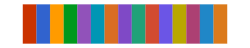

```mathematica
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[24,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=24;
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[112,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=112;
```

```mathematica
ColorData[colorselecitonumber][1]
```

RGBColor[0.790588, 0.201176, 0.]

## Plot

```mathematica
data=Import[NotebookDirectory[]<>"EF04FitResult05192022.xlsx"];
```

```mathematica
tabnamecolumn♕={"δg_H^ZZ","δg_H^WW","δg_H^γγ","δg_H^Zγ","δg_(1, Z)","δκ_γ","λ_Z","δg_H^gg","δg_H^tt","δg_H^cc","δg_H^bb","δg_H^ττ","δg_H^μμ","δΓ_H","δg_(Z, L)^ee","δg_(Z, R)^ee","δg_W^eν","δg_(Z, L)^μμ","δg_(Z, R)^μμ","δg_W^μν","δg_(Z, L)^ττ","δg_(Z, R)^ττ","δg_W^τν","δg_(Z, L)^uu","δg_(Z, R)^uu","δg_(Z, L)^dd","δg_(Z, R)^dd","δg_(Z, L)^bb","δg_(Z, R)^bb"};
```

```mathematica
selectiontoplot={1,2,3,4,8,9,10,11,12,13,14}
```

{1,2,3,4,8,9,10,11,12,13,14}

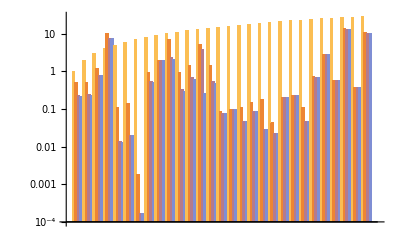

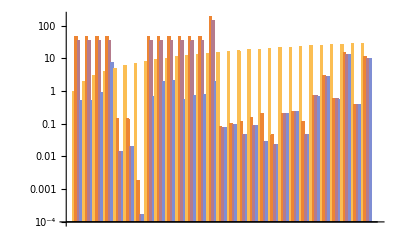

```mathematica
BarChart[{#[[1]],#[[-3]],#[[-2]],#[[-1]]}&/@data[[1]],ScalingFunctions->"Log",PlotRange->{10^-4,1}]
BarChart[{#[[1]],#[[-3]],#[[-2]],#[[-1]]}&/@data[[2]],ScalingFunctions->"Log",PlotRange->{10^-4,1}]
```

```mathematica
Dimensions[data[[1]]]
```

{29,18}

```mathematica
Table[({#[[2]],#[[-3]],#[[-2]],#[[-1]]}&/@data[[1]])[[i]],{i,selectiontoplot}]
Table[({#[[2]],#[[-3]],#[[-2]],#[[-1]]}&/@data[[2]])[[i]],{i,selectiontoplot}]
```

{{2.2,0.52,0.23,0.22},{2.,0.52,0.24,0.23},{2.4,1.2,0.79,0.79},{11.,10.,7.3,7.3},{1.8,0.94,0.54,0.52},{2.2,1.9,1.9,1.9},{100000.,7.2,2.3,2.1},{4.4,0.93,0.33,0.3},{2.3,1.4,0.68,0.6},{5.6,5.1,3.8,0.26},{5.6,1.4,0.54,0.49}}

{{180.,47.,34.,0.53},{180.,47.,34.,0.53},{180.,47.,34.,0.93},{180.,47.,34.,7.3},{180.,47.,34.,0.69},{180.,47.,34.,1.9},{100000.,48.,35.,2.1},{180.,47.,34.,0.55},{180.,47.,34.,0.72},{180.,48.,35.,0.76},{710.,190.,140.,2.}}

```mathematica
Table[({#[[2]],#[[-3]],#[[-2]],#[[-1]]}&/@data[[1]])[[i]]/100,{i,selectiontoplot}]
datatoplot1=Transpose[Table[If[%[[j,k]]>0.3,0.3,%[[j,k]]],{k,1,4},{j,1,Length[selectiontoplot]}]]
Table[({#[[2]],#[[-3]],#[[-2]],#[[-1]]}&/@data[[2]])[[i]]/100,{i,selectiontoplot}]
datatoplot2=Transpose[Table[If[%[[j,k]]>0.3,0.3,%[[j,k]]],{k,1,4},{j,1,Length[selectiontoplot]}]]
```

{{0.022,0.0052,0.0023,0.0022},{0.02,0.0052,0.0024,0.0023},{0.024,0.012,0.0079,0.0079},{0.11,0.1,0.073,0.073},{0.018,0.0094,0.0054,0.0052},{0.022,0.019,0.019,0.019},{1000.,0.072,0.023,0.021},{0.044,0.0093,0.0033,0.003},{0.023,0.014,0.0068,0.006},{0.056,0.051,0.038,0.0026},{0.056,0.014,0.0054,0.0049}}

{{0.022,0.0052,0.0023,0.0022},{0.02,0.0052,0.0024,0.0023},{0.024,0.012,0.0079,0.0079},{0.11,0.1,0.073,0.073},{0.018,0.0094,0.0054,0.0052},{0.022,0.019,0.019,0.019},{0.3,0.072,0.023,0.021},{0.044,0.0093,0.0033,0.003},{0.023,0.014,0.0068,0.006},{0.056,0.051,0.038,0.0026},{0.056,0.014,0.0054,0.0049}}

{{1.8,0.47,0.34,0.0053},{1.8,0.47,0.34,0.0053},{1.8,0.47,0.34,0.0093},{1.8,0.47,0.34,0.073},{1.8,0.47,0.34,0.0069},{1.8,0.47,0.34,0.019},{1000.,0.48,0.35,0.021},{1.8,0.47,0.34,0.0055},{1.8,0.47,0.34,0.0072},{1.8,0.48,0.35,0.0076},{7.1,1.9,1.4,0.02}}

{{0.3,0.3,0.3,0.0053},{0.3,0.3,0.3,0.0053},{0.3,0.3,0.3,0.0093},{0.3,0.3,0.3,0.073},{0.3,0.3,0.3,0.0069},{0.3,0.3,0.3,0.019},{0.3,0.3,0.3,0.021},{0.3,0.3,0.3,0.0055},{0.3,0.3,0.3,0.0072},{0.3,0.3,0.3,0.0076},{0.3,0.3,0.3,0.02}}

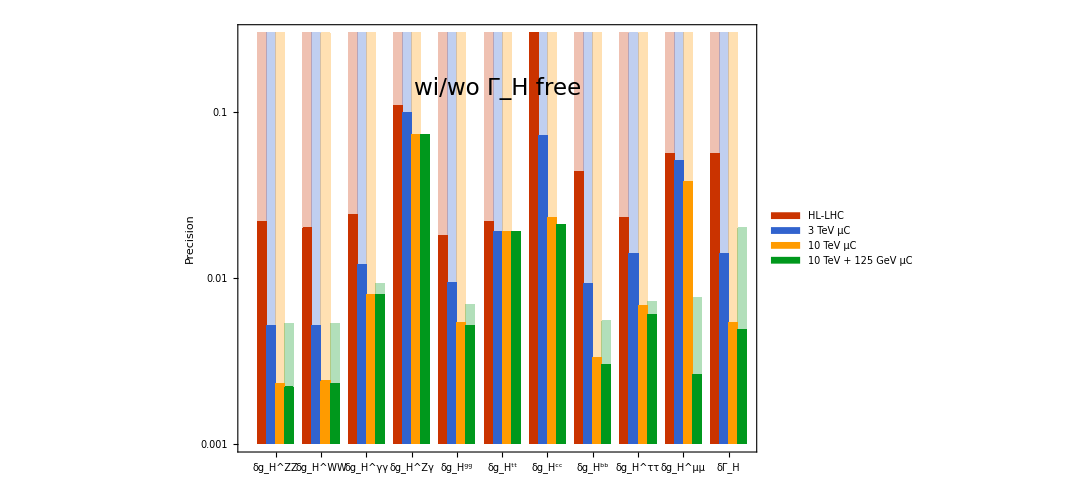

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0.1,Background->Directive[White,Opacity[0.8]]]
Show[
BarChart[datatoplot2,ScalingFunctions->"Log",Frame->True,ChartLabels->{Table[tabnamecolumn♕[[i]],{i,selectiontoplot}],None},FrameLabel->{{"Precision",None},{None,Style["Muon Collider Higgs Precision Projections (SMEFT)",23]}},FrameStyle->Directive[Black,Thick],GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Directive[EdgeForm[None],Opacity[0.3],ColorData[colorselecitonumber][#]]&/@{1,2,3,4,5}},BaseStyle->28,PlotRange->{{0.5,55.5},{10^-3,0.3}},BarSpacing->{0,1},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->{0,0},ImageSize->800,Epilog->{Inset[SwatchLegend[ColorData[colorselecitonumber][#]&/@{1,2,3,4},Style[#,20,FontFamily->"CMU Serif"]&/@{"HL-LHC","3 TeV μC","10 TeV μC","10 TeV + 125 GeV μC"},LegendFunction->frame,LegendMargins->5,LegendMarkerSize->25, Spacings->0.5,LegendLayout->"Row"],Scaled[{0.32,0.89}]],Inset[Style["wi/wo Γ_H free",23],Scaled[{0.5,0.85}]]}],BarChart[datatoplot1,ScalingFunctions->"Log",Frame->True,FrameStyle->Black,ChartStyle->{Directive[EdgeForm[None],ColorData[colorselecitonumber][#]]&/@{1,2,3,4,5}},BaseStyle->12,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1},FrameTicks->{LinTicks,LinTicks,LinTicks,LogTicks},PlotRangePadding->{0,0}]
]
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0.1,Background->Opacity[0.5]]
```

```mathematica
SwatchLegend[ColorData[colorselecitonumber][#]&/@{1,2,3,4},Style[#,FontFamily->"CMU Serif"]&/@{"HL-LHC","3 TeV μC","10 TeV μC","3 TeV + 125 GeV μC"},LegendFunction->frame,LegendMargins->2,LegendMarkerSize->25, Spacings->0.5,LegendLayout->"Row"]
```